# 2D Graphics Primitives

Math 250 - Math with Mathematica
Christopher Hanusa

## Comprehension Questions

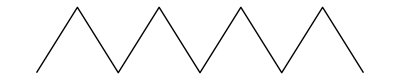
### 8-1. Instead of typing each coordinate (as in the tutorial), use a Table command to create this ZigZag pattern: -Graphics-

#### Hint 1 (Expand cell to see)

Use the first coordinate as the indexing variable in your Table command to get the list:

```mathematica
{{0,0},{1,1},{2,0},{3,1},{4,0},{5,1},{6,0},{7,1},{8,0}}
```

#### Hint 2 (Expand cell to see)

Use an If statement and a Q command to condition on whether the first entry is even or odd.

### 8-2. Modify your code from Question 8-1 to make the zigzag pattern longer (from (0,0) to (100,0)), using a thick purple line!

### 8-3. Use Table commands to draw a grid of vertical and horizontal lines that looks like graph paper, just like this.

-Graphics-

#### Hint 1 (Expand cell to see)

Combine one Table command for the horizontal line segments and one Table command for the vertical line segments.

#### Hint 2 (Expand cell to see)

How do you create TWO parallel horizontal lines?  What changed from line one to line two?  Use this to figure out what your indexing variable should be in the Table command.

### 8-4. Create a red square with black boundary and also put a blue circle on the boundary of the square.

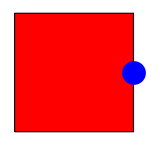

### 8-5. For this list of pairs of coordinate pairs, use the Map command to display all the corresponding line segments.

```mathematica
segments={{{0,0},{1,0}},{{1/2,0},{1/2,1}},{{1/2,1/2},{-1/2,1/2}},{{0,1/2},{0,-1/2}}}
```

### 8-6. Now add small circles on the endpoints of all the line segments from Question 7.

#### Hint 1.

Use the Flatten and Map commands.

#### Hint 2.

Make sure to use the additional option Flatten[ • , 1]

### 8-7. Create a circle of circles like this:

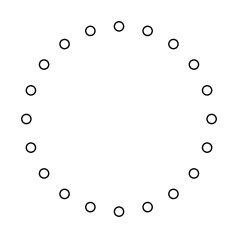

## Challenge Questions

### 8-X1. Create a discrete spiral that visits points that get further and further away from the origin, similar to this:

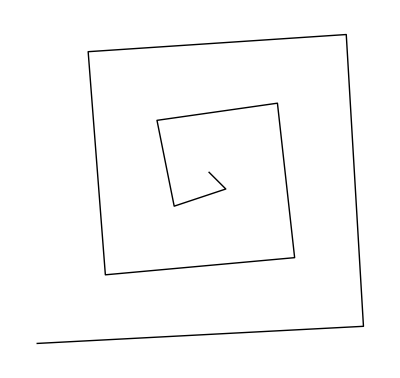

#### Hint:

The points in the given spiral are:

{{0,0},{1,-1},{-2,-2},{-3,3},{4,4},{5,-5},{-6,-6},{-7,7},{8,8},{9,-9},{-10,-10}}

### 8-X2. Comprehension Question 8-3 asked you to draw a grid of vertical and horizontal lines that looks like graph paper, just like this. Make sure everyone is on the same page to create it.

-Graphics-

### Color the lines in the grid in either rainbow or random colors, like this:

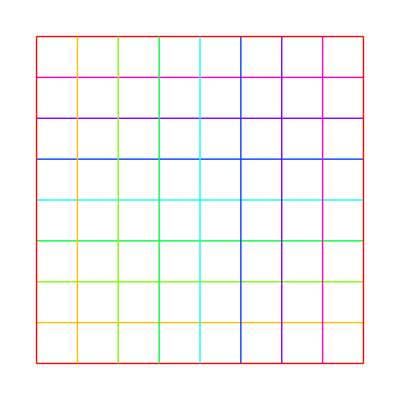
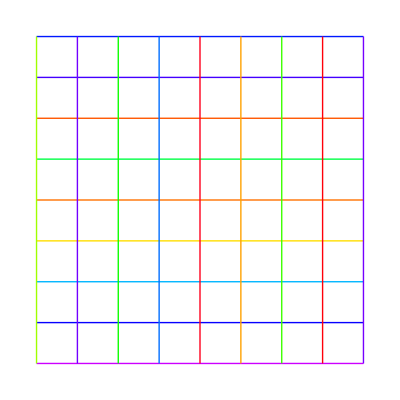

### 8-X3. Now, instead of coloring the lines, put colored circles inside every square of the grid.

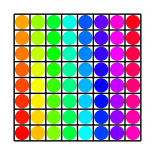

### 8-X4. Using the technique for making a regular polygon using trigonometry, make a star.

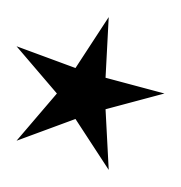

### 8-X5. When we created regular n-gons using trigonometry, we drew the n points on the circle and connected each vertex with its two neighbors. What will happen if you instead connect each vertex not with its neighbors but with the neighbors of its neighbors (distance two away)? Or further away?